```mathematica
h:=1/2(k11 Jx^(3/2) Sqrt[Jy]+k12 Sqrt[Jx] Jy^(3/2))(Cos[ϕx-ϕy+η n 2π])+3/8(p Jx^2+r Jy^2+2 q Jx Jy)+3/4f2 Jx Jy (Cos[2ϕx-2ϕy+2η n 2π])+k1 Cos[ϕx+2 π s(νx+νy+η)/2-wr s]Sqrt[Jx]+k2 Cos[ϕy+2 π s(νx+νy-η)/2-wr s]Sqrt[Jy]
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2,k11->k11,k12->k12,p->p,r->r,q->q,η->η,n->t,k1->k1,k2->k2,νx->νx,νy->νy,wr->wr,s->t});
```

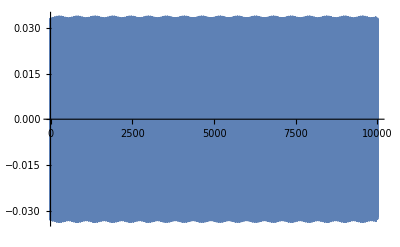

```mathematica
inloc=inputpr/.{Jxv->a 0.0002,Jyv->b 0.0002,ϕxv->ϕa,ϕyv->ϕb,f2->0,k11->-50,k12->50,p->0,r->0,q->-0,η->0.001,k1->.0,k2->.0,νx->.1705,νy->.1695,wr->.1715,n->t};
tablesol=Table[Flatten[NDSolve[inloc/.{a->a,b->1-a,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]],{a,0.055,0.955,0.15}];
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
tablea=Table[Table[{t1,podsum[[i]]},{t1,0,100000,1}],{i,1,7}];
ListPlot[(tablea[[1]])[[Range[10000]]],Joined->True,PlotRange->All]
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tableb=Table[Table[{t1,podsumb[[i]]},{t1,0,100000,1}],{i,1,7}];
a1= Table[(tablea[[i]])[[All,2]],{i,1,7}];
b1=Table[(tableb[[i]])[[All,2]],{i,1,7}];
```

```mathematica
xwind=Table[Table[(Sin[i π/100000])^2 a1[[j,i]],{i,0,100000}],{j,1,7}];
ywind=Table[Table[(Sin[i π/100000])^2 b1[[j,i]],{i,0,100000}],{j,1,7}];
```

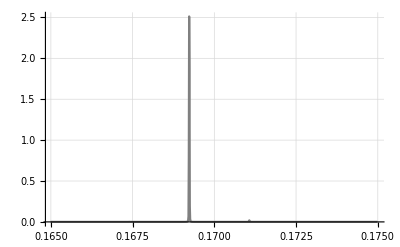
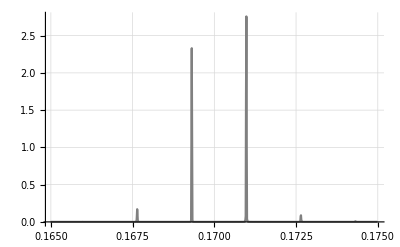
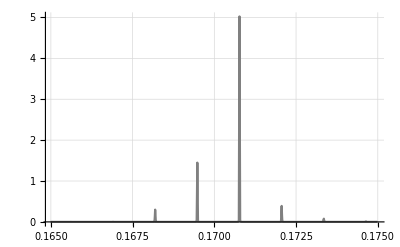
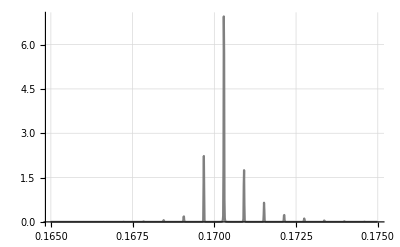
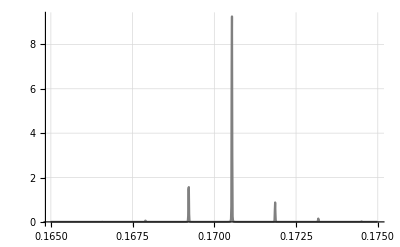
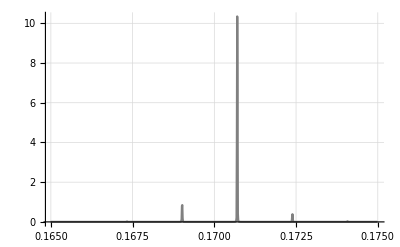
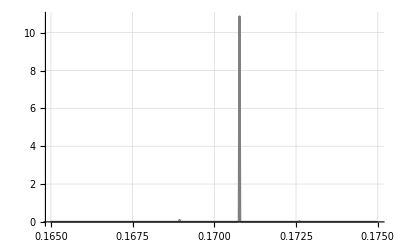

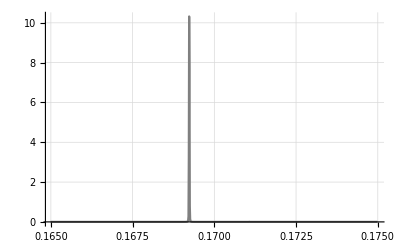

```mathematica
listfourierx=Table[Abs[Fourier[xwind[[i]]]],{i,1,7}];
listfouriery=Table[Abs[Fourier[ywind[[i]]]],{i,1,7}];
Table[ListPlot[Table[{(n1-1)/(100000),listfourierx[[i,n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]] ,{i,1,7}]
Table[ListPlot[Table[{(n1-1)/(100000),listfouriery[[i,n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]],{i,1,7}]
Table[ListPlot[Table[{(n1-1)/(100000),Log[listfouriery[[i,n1]]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 8]],{i,1,7}]
```

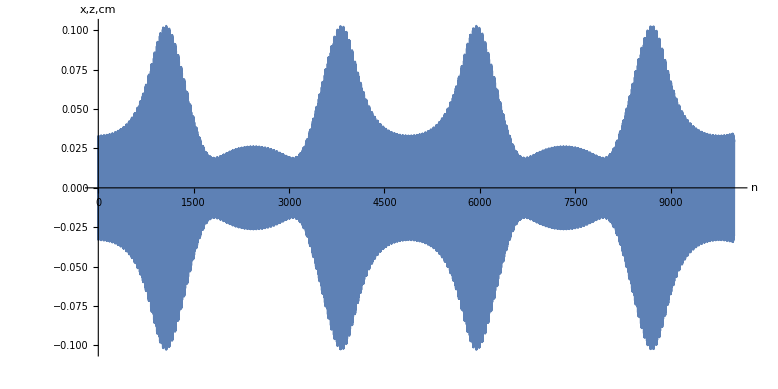

```mathematica
ListPlot[(tablea[[2]])[[Range[10000]]],Joined->True,PlotRange->All,AspectRatio->1/2,AxesLabel->{"n","x,z,cm"},LabelStyle->Directive[Black, 20]]
```

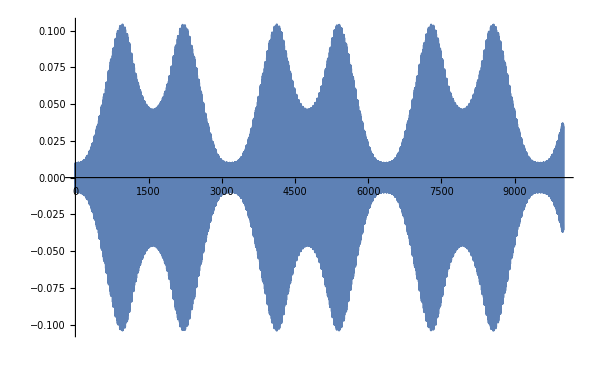

```mathematica
inloc=inputpr/.{Jxv->a 0.0002,Jyv->b 0.0002,ϕxv->ϕa,ϕyv->ϕb,f2->20,p->10,q->-15,r->40,k11->-20,k12->10,k1->0,k2->0,η->0.001,n->t};
tablesol=Table[Flatten[NDSolve[inloc/.{a->a,b->1-a,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]],{a,0.005,0.305,0.05}];
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
tablea=Table[Table[{t1,podsum[[i]]},{t1,0,100000,1}],{i,1,7}];
ListPlot[(tablea[[1]])[[Range[10000]]],Joined->True,PlotRange->All]
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

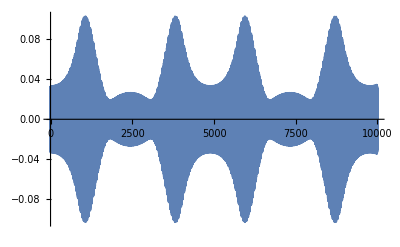

```mathematica
ListPlot[(tablea[[2]])[[Range[10000]]],Joined->True,PlotRange->All]
```

```mathematica
tableb=Table[Table[{t1,podsumb[[i]]},{t1,0,100000,1}],{i,1,7}];
a1= Table[(tablea[[i]])[[All,2]],{i,1,7}];
b1=Table[(tableb[[i]])[[All,2]],{i,1,7}];
```

```mathematica
xwind=Table[Table[(Sin[i π/100000])^2 a1[[j,i]],{i,0,100000}],{j,1,7}];
ywind=Table[Table[(Sin[i π/100000])^2 b1[[j,i]],{i,0,100000}],{j,1,7}];
```

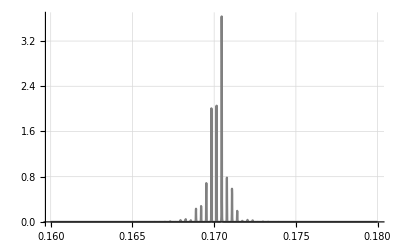
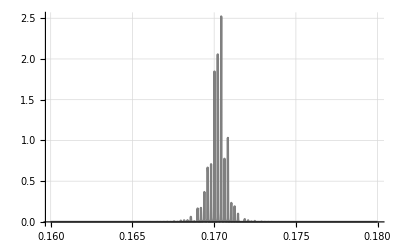
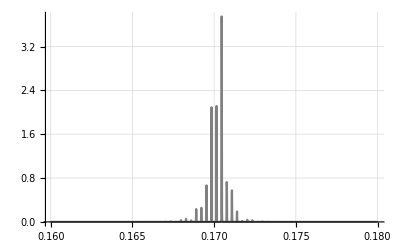
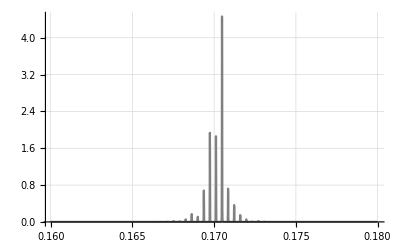
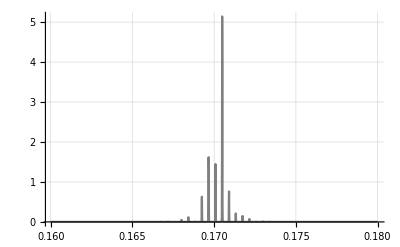
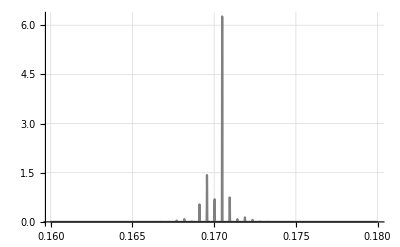
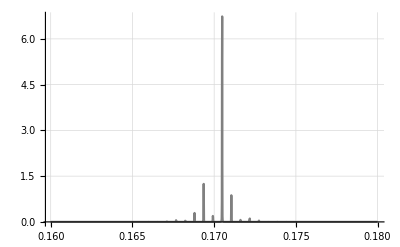

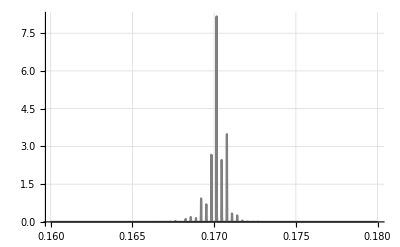

```mathematica
listfourierx=Table[Abs[Fourier[xwind[[i]]]],{i,1,7}];
listfouriery=Table[Abs[Fourier[ywind[[i]]]],{i,1,7}];
Table[ListPlot[Table[{(n1-1)/(100000),listfourierx[[i,n1]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]] ,{i,1,7}]
Table[ListPlot[Table[{(n1-1)/(100000),listfouriery[[i,n1]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]],{i,1,7}]
```

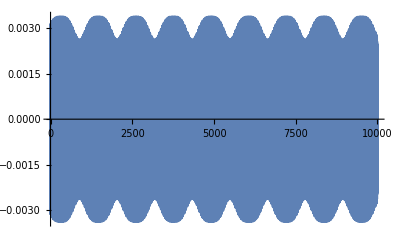

```mathematica
inloc=inputpr/.{Jxv->a 0.00002,Jyv->b 0.00002,ϕxv->ϕa,ϕyv->ϕb,f2->20,p->10,q->-15,r->40,k11->-20,k12->10,k1->0,k2->0,η->0.001,n->t};
tablesol=Table[Flatten[NDSolve[inloc/.{a->a,b->1-a,ϕa->π/2,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]],{a,0.005,0.305,0.05}];
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π/2,ϕb->0};
tablea=Table[Table[{t1,podsum[[i]]},{t1,0,100000,1}],{i,1,7}];
ListPlot[(tablea[[1]])[[Range[10000]]],Joined->True,PlotRange->All]
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π/2,ϕb->0};
```

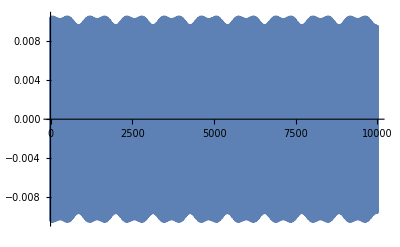

```mathematica
ListPlot[(tablea[[2]])[[Range[10000]]],Joined->True,PlotRange->All]
```

```mathematica
tableb=Table[Table[{t1,podsumb[[i]]},{t1,0,100000,1}],{i,1,7}];
a1= Table[(tablea[[i]])[[All,2]],{i,1,7}];
b1=Table[(tableb[[i]])[[All,2]],{i,1,7}];
```

```mathematica
xwind=Table[Table[(Sin[i π/100000])^2 a1[[j,i]],{i,0,100000}],{j,1,7}];
ywind=Table[Table[(Sin[i π/100000])^2 b1[[j,i]],{i,0,100000}],{j,1,7}];
```

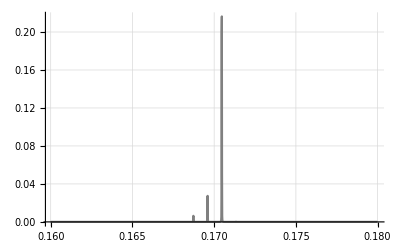
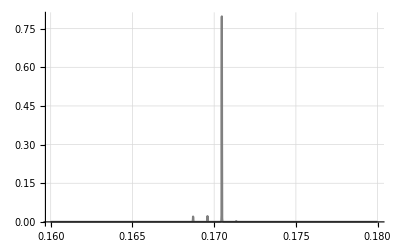
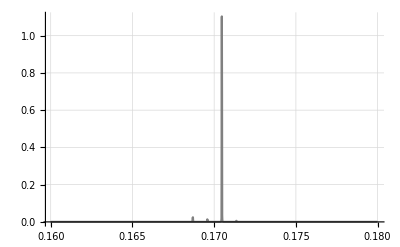
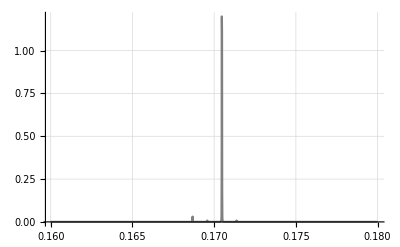
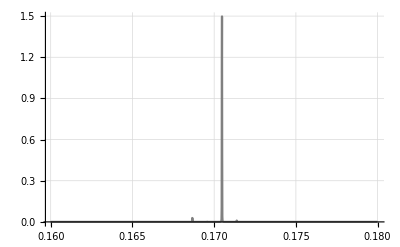
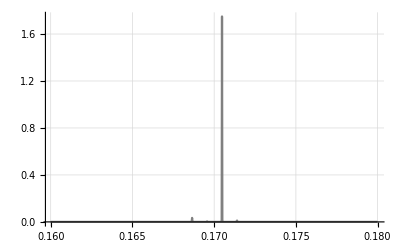
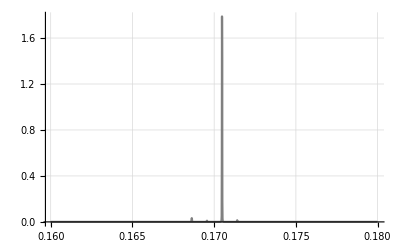

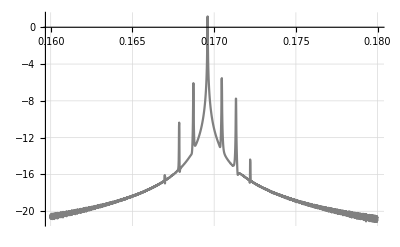

```mathematica
listfourierx=Table[Abs[Fourier[xwind[[i]]]],{i,1,7}];
listfouriery=Table[Abs[Fourier[ywind[[i]]]],{i,1,7}];
Table[ListPlot[Table[{(n1-1)/(100000),listfourierx[[i,n1]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]] ,{i,1,7}]
Table[ListPlot[Table[{(n1-1)/(100000),Log[listfouriery[[i,n1]]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]],{i,1,7}]
```

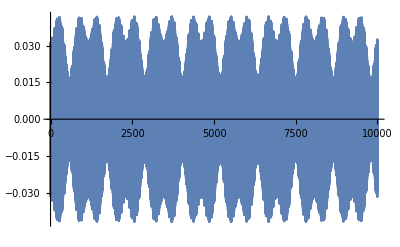

```mathematica
inloc=inputpr/.{Jxv->a 0.0002,Jyv->b 0.0002,ϕxv->ϕa,ϕyv->ϕb,f2->20,p->30,q->-60,r->-50,k11->-20,k12->10,k1->0,k2->0,η->0.001,n->t};
tablesol=Table[Flatten[NDSolve[inloc/.{a->a,b->1-a,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]],{a,0.05,0.95,0.15}];
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
tablea=Table[Table[{t1,podsum[[i]]},{t1,0,100000,1}],{i,1,7}];
ListPlot[(tablea[[1]])[[Range[10000]]],Joined->True,PlotRange->All]
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

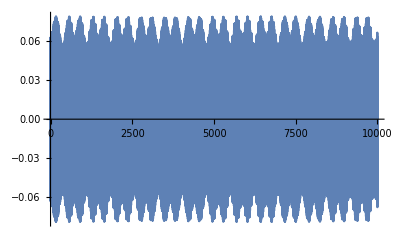

```mathematica
ListPlot[(tablea[[2]])[[Range[10000]]],Joined->True,PlotRange->All]
```

```mathematica
tableb=Table[Table[{t1,podsumb[[i]]},{t1,0,100000,1}],{i,1,7}];
a1= Table[(tablea[[i]])[[All,2]],{i,1,7}];
b1=Table[(tableb[[i]])[[All,2]],{i,1,7}];
```

```mathematica
xwind=Table[Table[(Sin[i π/100000])^2 a1[[j,i]],{i,0,100000}],{j,1,7}];
ywind=Table[Table[(Sin[i π/100000])^2 b1[[j,i]],{i,0,100000}],{j,1,7}];
```

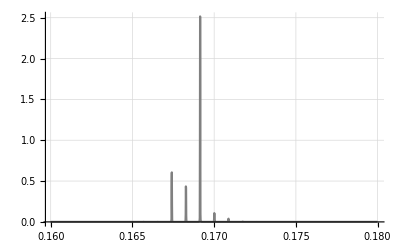
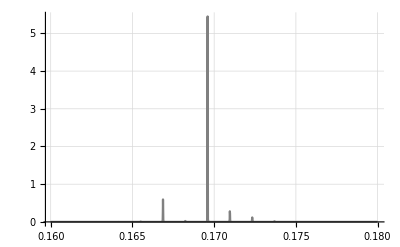
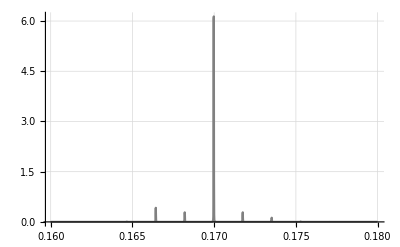
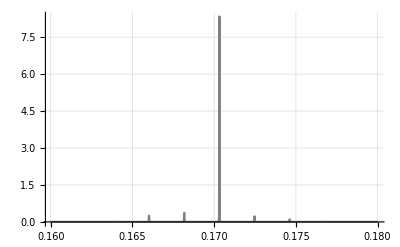
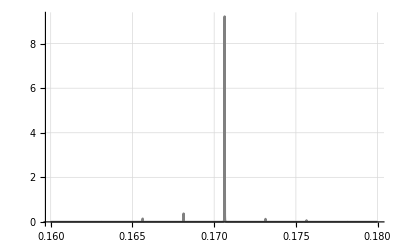
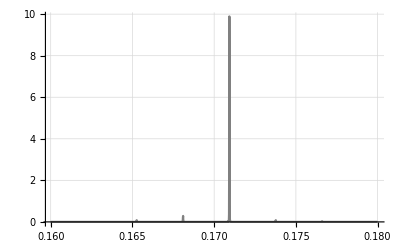
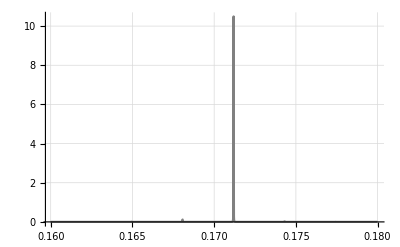

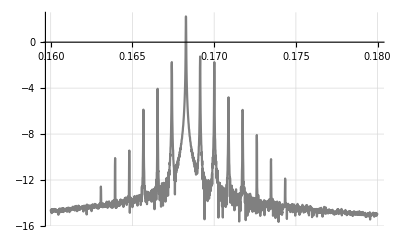

```mathematica
listfourierx=Table[Abs[Fourier[xwind[[i]]]],{i,1,7}];
listfouriery=Table[Abs[Fourier[ywind[[i]]]],{i,1,7}];
Table[ListPlot[Table[{(n1-1)/(100000),listfourierx[[i,n1]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]] ,{i,1,7}]
Table[ListPlot[Table[{(n1-1)/(100000),Log[listfouriery[[i,n1]]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]],{i,1,7}]
```

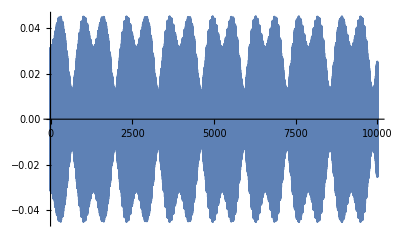

```mathematica
inloc=inputpr/.{Jxv->a 0.0002,Jyv->b 0.0002,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->-50,k12->50,p->0,r->0,q->-0,k1->0,k2->0,η->0.001,n->t};
tablesol=Table[Flatten[NDSolve[inloc/.{a->a,b->1-a,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]],{a,0.05,0.95,0.15}];
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
tablea=Table[Table[{t1,podsum[[i]]},{t1,0,100000,1}],{i,1,7}];
ListPlot[(tablea[[1]])[[Range[10000]]],Joined->True,PlotRange->All]
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

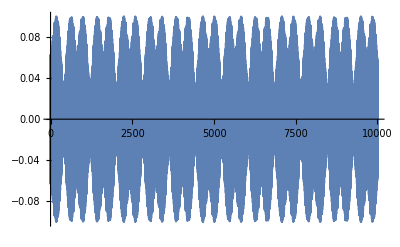

```mathematica
ListPlot[(tablea[[2]])[[Range[10000]]],Joined->True,PlotRange->All]
```

```mathematica
tableb=Table[Table[{t1,podsumb[[i]]},{t1,0,100000,1}],{i,1,7}];
a1= Table[(tablea[[i]])[[All,2]],{i,1,7}];
b1=Table[(tableb[[i]])[[All,2]],{i,1,7}];
```

```mathematica
xwind=Table[Table[(Sin[i π/100000])^2 a1[[j,i]],{i,0,100000}],{j,1,7}];
ywind=Table[Table[(Sin[i π/100000])^2 b1[[j,i]],{i,0,100000}],{j,1,7}];
```

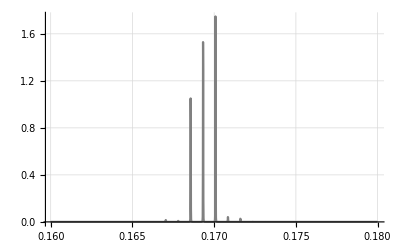
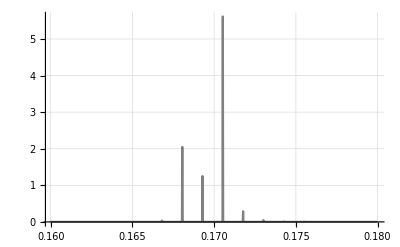
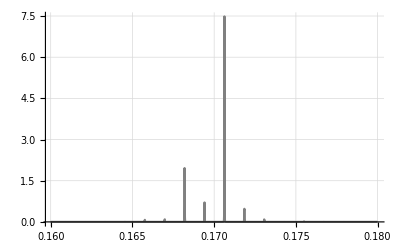
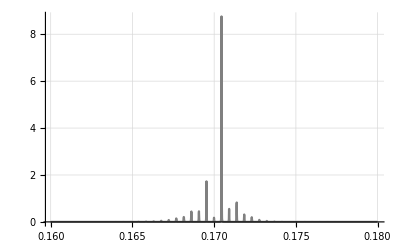
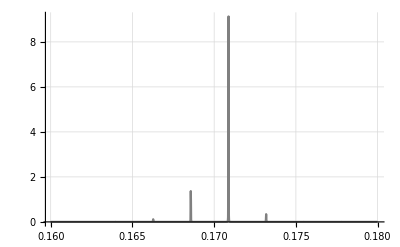
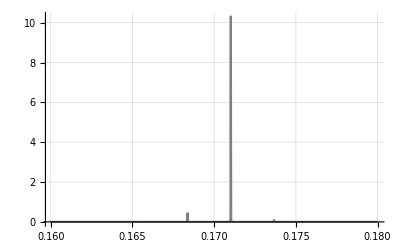
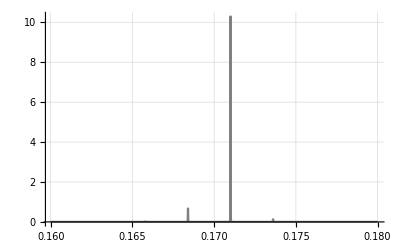

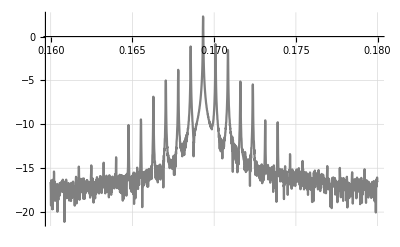

```mathematica
listfourierx=Table[Abs[Fourier[xwind[[i]]]],{i,1,7}];
listfouriery=Table[Abs[Fourier[ywind[[i]]]],{i,1,7}];
Table[ListPlot[Table[{(n1-1)/(100000),listfourierx[[i,n1]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]] ,{i,1,7}]
Table[ListPlot[Table[{(n1-1)/(100000),Log[listfouriery[[i,n1]]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]],{i,1,7}]
```

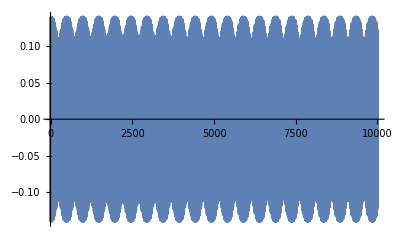

```mathematica
inloc=inputpr/.{Jxv->a 0.0002,Jyv->b 0.0002,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->-50,k12->50,p->0,r->0,q->-0,k1->0,k2->0,η->0.001,n->t};
tablesol=Table[Flatten[NDSolve[inloc/.{a->a,b->1-a,ϕa->0,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]],{a,0.995,0.695,-0.05}];
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->0,ϕb->0};
tablea=Table[Table[{t1,podsum[[i]]},{t1,0,100000,1}],{i,1,7}];
ListPlot[(tablea[[1]])[[Range[10000]]],Joined->True,PlotRange->All]
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->0,ϕb->0};
```

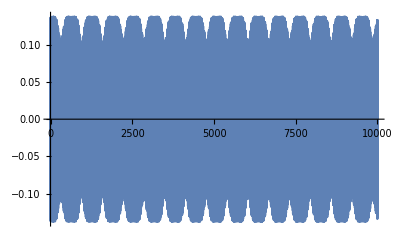

```mathematica
ListPlot[(tablea[[2]])[[Range[10000]]],Joined->True,PlotRange->All]
```

```mathematica
tableb=Table[Table[{t1,podsumb[[i]]},{t1,0,100000,1}],{i,1,7}];
a1= Table[(tablea[[i]])[[All,2]],{i,1,7}];
b1=Table[(tableb[[i]])[[All,2]],{i,1,7}];
```

```mathematica
xwind=Table[Table[(Sin[i π/100000])^2 a1[[j,i]],{i,0,100000}],{j,1,7}];
ywind=Table[Table[(Sin[i π/100000])^2 b1[[j,i]],{i,0,100000}],{j,1,7}];
```

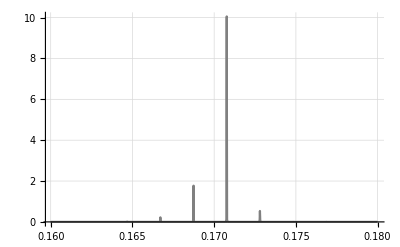
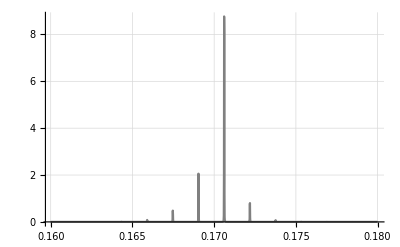
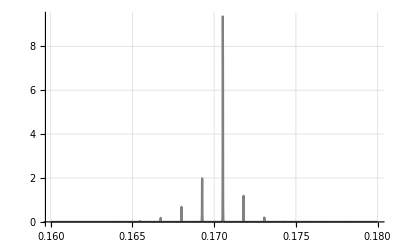
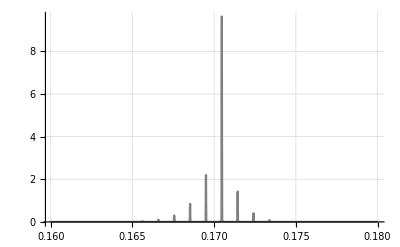
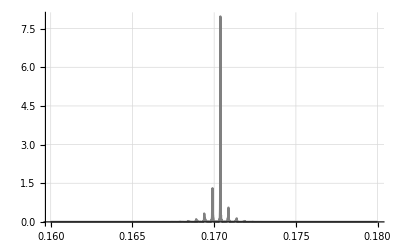
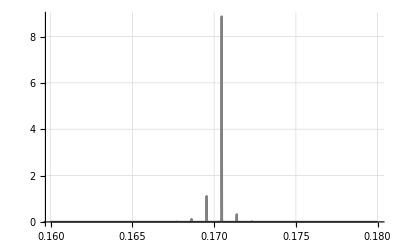
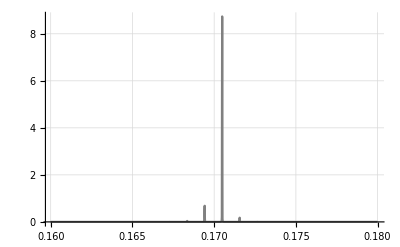

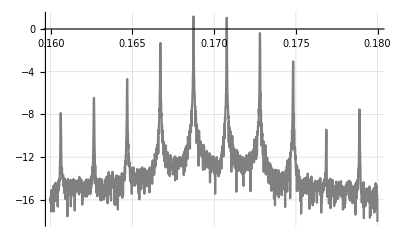

```mathematica
listfourierx=Table[Abs[Fourier[xwind[[i]]]],{i,1,7}];
listfouriery=Table[Abs[Fourier[ywind[[i]]]],{i,1,7}];
Table[ListPlot[Table[{(n1-1)/(100000),listfourierx[[i,n1]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]] ,{i,1,7}]
Table[ListPlot[Table[{(n1-1)/(100000),Log[listfouriery[[i,n1]]]},{n1,1,100001}][[Range[16000,18000]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic,LabelStyle->Directive[Black, 10]],{i,1,7}]
```